Generate Data

```mathematica
Simulatek[θ_,nsites_,ntemplates_]:={#,ntemplates-#}&/@RandomVariate[BetaBinomialDistribution[θ,θ,ntemplates],nsites]
```

MLE recursion

```mathematica
UpdateS[data_][s_]:=Block[{dat,ns,mk,f1,f2,a,c},
dat=Select[data,(Length[#]==2&&Total[#]>2)&];
If[Length[dat]<2,
Return[0.0],
mk={0.5,0.5};
ns=Total/@dat;
f1=Total[PolyGamma[s]-PolyGamma[ns+s]+((PolyGamma[(#+s mk)]-PolyGamma[s mk])&/@dat).mk];
f2=Total[PolyGamma[1,s]-PolyGamma[1,ns+s]+((PolyGamma[1,(#+s mk)]-PolyGamma[1,s mk])&/@dat).mk^2];
a=-s^2 f2;
c=f1-a/s;
If[c≥0,
a=s^3(s f2 + 2 f1);
c=-(s^2 f1+a/s);
];
Return[-a/c];]
]
```

```mathematica
FindS[data_]:=FixedPoint[UpdateS[data],0.01,SameTest->(Abs[#1-#2]<1*^-8&)]
```

```mathematica
FindNeutralθ[data_]:=1/2 FindS[data]
```

```mathematica
FindNeutralθ2[data_]:=N[Mean[Function[{a,b},Module[{x},
x=a/(a+b);
2x(1-x)]]@@@data]]
```

```mathematica
quintiles[θ_,nsites_,ntemplates_]:=Quantile[Table[FindNeutralθ[Simulatek[θ,nsites,ntemplates]],1000],{.1,.9}]
```

```mathematica
quintiles2[θ_,nsites_,ntemplates_]:=Quantile[Table[FindNeutralθ2[Simulatek[θ,nsites,ntemplates]],1000],{.1,.9}]
```

```mathematica
QuintileLines[θtable_,qfun_,color_]:=Module[{lower,upper},
{lower,upper}=Transpose[Table[qfun[θ,100,100],{θ,θtable}]];
Graphics[{color,
Line[Map[Log10[Max[#,10^-6]]&,
Transpose[{θtable,lower}],
{2}]],
Line[Map[Log10[Max[#,10^-6]]&,
Transpose[{θtable,upper}],
{2}]],Opacity[.4],
Polygon[Join[
Map[Log10[Max[#,10^-6]]&,
Transpose[{θtable,upper}],
{2}],
Reverse[Map[Log10[Max[#,10^-6]]&,
Transpose[{θtable,lower}],
{2}]]
]
]
}]]
```

```mathematica
θtab = 10^Range[-2.5,0.5,.2];
```

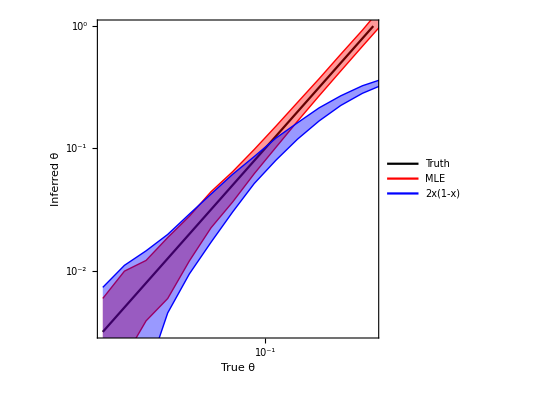

```mathematica
plt = Show[Plot[x,{x,-2.5,0},AspectRatio->1,PlotRange->{{-2.5,0},{-2.5,0}},FrameTicks->{{LogTicks[-5,0],LogTicks[-5,0,ShowTickLabels->False]},{LogTicks[-5,0],LogTicks[-5,0,ShowTickLabels->False]}},FrameLabel->{"True θ","Inferred θ"},PlotLegends->Placed[LineLegend[{Black,Red,Blue},{"Truth","MLE","2x(1-x)"}],{.25,.8}],PlotStyle->Black],QuintileLines[θtab,quintiles,Red],QuintileLines[θtab,quintiles2,Blue]]
```

```mathematica
ImExport["mle_vs_var",plt,{1,1}]
```

Figures/mle_vs_var.pdf